```mathematica
April 1, 2015 -- Taylor 12.3, 12.4, 12.7

The following code (for the driven damped pendulum) is 
what we developed in class.  It can be used to reproduce 
the examples in Taylor 12.3, 12.4, and 12.7.

Important Points:
(1) For low GAMMA, there is a single attractor.
(2) As GAMMA is increased, there is a cascade of period-doubling.
(3) After the period-doubling, there is chaos.
```

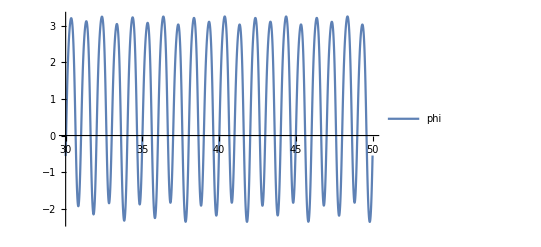

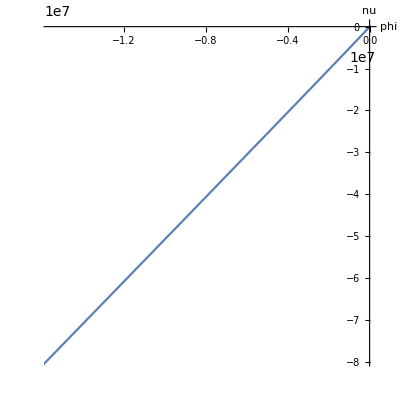

```mathematica
GAMMA=1.0830;
OMEGA=2*Pi;
OMEGA0=1.5*OMEGA;
BETA=OMEGA0/4;
PHIDOT = phi'[t]==nu[t];
NUDOT = nu'[t]==-2*BETA*nu[t]-OMEGA0^2*Sin[phi[t]]+GAMMA*OMEGA0^2*Cos[OMEGA*t];
NU0 = nu[0]==0;
PHI0 = phi[0]== -Pi/2;
SOLUTION = NDSolve[{PHIDOT,NUDOT,NU0,PHI0},{phi,nu},{t,0,100}];
EPHI = Evaluate[phi[t]/.SOLUTION];
ENU = Evaluate[nu[t]/.SOLUTION];
EPHINU = Evaluate[{phi[t],nu[t]}/.SOLUTION];
Plot[{EPHI,ENU},{t,0,5},PlotRange->All,ImageSize->Scaled[0.5],PlotLegends->{"phi","nu"}];
Plot[EPHI, {t,30,50}, PlotRange-> All, ImageSize -> Scaled[0.5],PlotLegends -> {"phi"}]
Plot[EPHI, {t,50,70}, PlotRange->{-2.4,-1.6}, ImageSize -> Scaled[0.5], PlotLegends ->("phi")];
ParametricPlot[EPHINU,{t,30,150},AspectRatio->1,AxesLabel->{phi,nu}]
```